```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
metabsim=metabgensteadystate[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{472.106,Null}

```mathematica
keepMetabSS=keepallmetabmaintainsteadystate[metabsim[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1181.14,Null}

```mathematica
metabsimMemory=metabproteinmemfast[keepMetabSS];
```

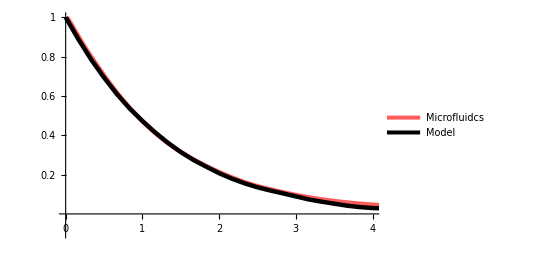

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1mmmcACF30minwindowsmooth]}],iptg1mmmcACF30minwindowsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[1]]]},PlotRange->{{0,4},{-.1,1}},PlotLegends->Placed[{"Microfluidcs","Model"},Right],PlotStyle->{{Thickness[0.008],RGBColor[1,0.36,0.36]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
{iptg1000um630growthACFsmooth,iptg1000um630mcACFsmooth,iptg1000um630betaxACFsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1000um630ACFsmooth.txt","Table"];
```

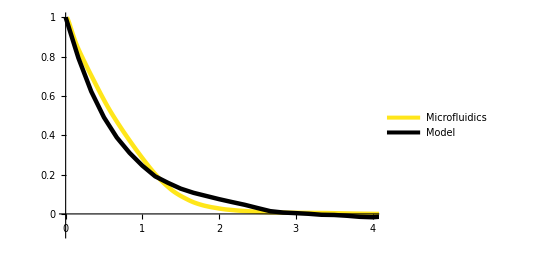

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1000um630betaxACFsmooth]}],iptg1000um630betaxACFsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[3]]]},PlotRange->{{0,4},{-.1,1}},
PlotLegends->Placed[{"Microfluidics","Model"},Right],
PlotStyle->{{Thickness[0.008],RGBColor[1,0.9,0.1]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0,0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

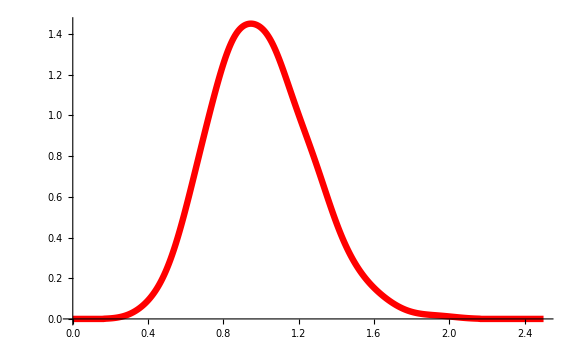

```mathematica
SmoothHistogram[keepMetabSS[[37,5]]/Mean[keepMetabSS[[37,5]]],.09,PlotStyle->{Thickness[0.008],Red},PlotRange->{{0,2.5},Automatic},ImageSize->Large]
```

```mathematica
exp630rawdata=Import["Z:\\Alex\\mfv2\\6-30-2020 tifs\\1000um iptg\\1000umclistaltalt.txt","Table"];//AbsoluteTiming
```

{1.688,Null}

```mathematica
MatrixForm[exp630rawdata[[1;;5]]]
```

({Cell,ID,Mother,ID,Time,(Frames),Age,(Frames),Relative,Age,Cell,age,Long,axis,(L),Short,axis,Area,Fluor1,sum,Fluor1,mean,Fluor2,sum,Fluor2,mean,Num,of,neighbors,dL,max,dL,min,Generation,Generation0,Growth,Rate}
{1044,40,2,1,0.0526316,18,18,7.02643,127,213108,1678.02,160647,1264.94,NaN,2,-1,1,1,0.0111484}
{1044,40,3,2,0.105263,18,18,6.98987,126,209972,1666.44,157056,1246.48,NaN,2,-1,1,1,0.0111484}
{1044,40,4,3,0.157895,18,18,7.25622,131,215520,1645.19,168914,1289.42,NaN,2,-1,1,1,0.0111484}
{1044,40,5,4,0.210526,18,18,7.30657,132,221393,1677.22,170253,1289.8,NaN,2,-1,1,1,0.0111484})

```mathematica
exp630rawdataselect=exp630rawdata[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
MatrixForm[exp630rawdataselect[[1;;5]]]
```

(Cell | ID | Mother | (Frames) | Age | Relative | Age | Cell | age | Long
1044 | 40 | 2 | 18 | 18 | 127 | 213108 | 1678.02 | 160647 | 1264.94
1044 | 40 | 3 | 18 | 18 | 126 | 209972 | 1666.44 | 157056 | 1246.48
1044 | 40 | 4 | 18 | 18 | 131 | 215520 | 1645.19 | 168914 | 1289.42
1044 | 40 | 5 | 18 | 18 | 132 | 221393 | 1677.22 | 170253 | 1289.8)

```mathematica
exp630raw=exp630rawdataselect;
```

```mathematica
exp630raw[[2;;Length[exp630raw],{1,2,3,4,5,6}]]=Round[exp630raw[[2;;Length[exp630raw],{1,2,3,4,5,6}]]];
```

```mathematica
exp630raw[[2;;Length[exp630raw],{8}]]=N[exp630raw[[2;;Length[exp630raw],{8}]]-750];
```

```mathematica
exp630raw[[2;;Length[exp630raw],{10}]]=N[exp630raw[[2;;Length[exp630raw],{10}]]-963];
```

```mathematica
exp630raw[[2;;Length[exp630raw],{3}]]=N[exp630raw[[2;;Length[exp630raw],{3}]]*1/60];
```

```mathematica
MatrixForm[exp630raw[[1;;5]]]
```

(Cell | ID | Mother | (Frames) | Age | Relative | Age | Cell | age | Long
1044 | 40 | 0.0333333 | 18 | 18 | 127 | 213108 | 928.016 | 160647 | 301.937
1044 | 40 | 0.05 | 18 | 18 | 126 | 209972 | 916.444 | 157056 | 283.476
1044 | 40 | 0.0666667 | 18 | 18 | 131 | 215520 | 895.191 | 168914 | 326.42
1044 | 40 | 0.0833333 | 18 | 18 | 132 | 221393 | 927.22 | 170253 | 326.795)

```mathematica
exp630rawfljumpcut=removefljumps[exp630raw];//AbsoluteTiming
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

{8.94122,Null}

```mathematica
linsexp630=lineagefinder[exp630rawfljumpcut];//AbsoluteTiming
```

{11.7427,Null}

```mathematica
comblinexp630=combinelineages2fl[exp630raw,linsexp630];//AbsoluteTiming
```

{22.206,Null}

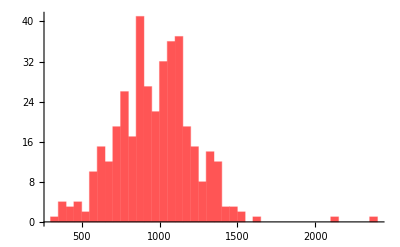

```mathematica
Histogram[Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]],50,PlotRange->All,ChartStyle->Lighter[Red]]
```

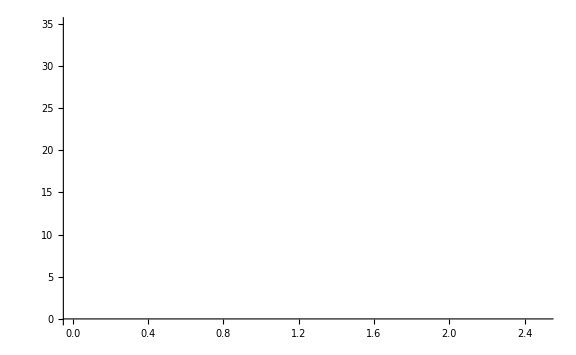
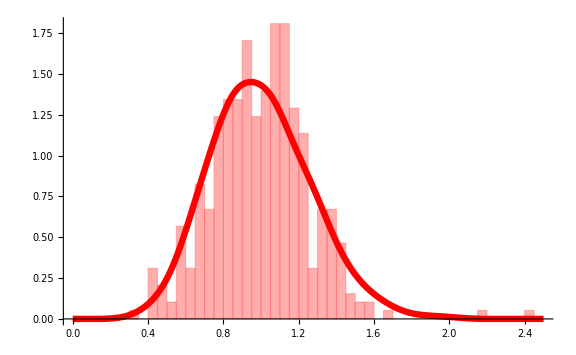

```mathematica
Overlay[{Histogram[{Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]]},30,PlotRange->{{0,2.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.36,0.36,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],30],Directive[Black,30]},ImageSize->Large],Show[{Histogram[{Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]]},30,"PDF",PlotRange->{{0,2.5},Automatic},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,30],Directive[RGBColor[0,0,0,0],30]},ImageSize->Large],SmoothHistogram[keepMetabSS[[37,5]]/Mean[keepMetabSS[[37,5]]],.09,PlotStyle->{Thickness[0.008],Red},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```

```mathematica
DOD=Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]];
```

```mathematica
StandardDeviation[DOD]
```

252.459

```mathematica
Mean[DOD]
```

972.179

```mathematica
noiseofDOD=(StandardDeviation[DOD]/Mean[DOD])^2
```

0.0674356

```mathematica
noiseofDODsim=(StandardDeviation[keepMetabSS[[37,5]]]/Mean[keepMetabSS[[37,5]]])^2
```

0.0673842

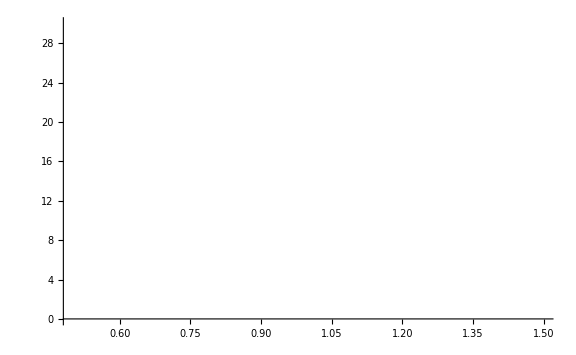
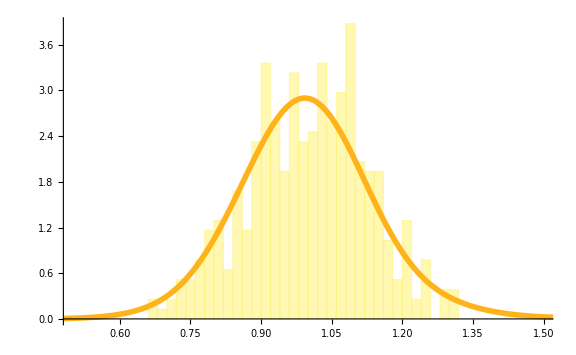

```mathematica
Overlay[{Histogram[{Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]]},30,PlotRange->{{0.5,1.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.95,0.4,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],30],Directive[Black,30]},ImageSize->Large],Show[{Histogram[{Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]]},30,"PDF",PlotRange->{{0.5,1.5},Automatic},ChartStyle->RGBColor[1,0.95,0.4],Axes->{True,True},AxesStyle->{Directive[Black,30],Directive[RGBColor[0,0,0,0],30]},ImageSize->Large],SmoothHistogram[keepMetabSS[[37,7]]/Mean[keepMetabSS[[37,7]]],.09,PlotStyle->{Thickness[0.007],RGBColor[1,0.7,0.1]},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```

```mathematica
Betax=Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]];
```

```mathematica
StandardDeviation[Betax]
```

44.4632

```mathematica
Mean[Betax]
```

346.29

```mathematica
noiseofbetax=(StandardDeviation[Betax]/Mean[Betax])^2
```

0.0164863

```mathematica
noiseofbetaxsim=(StandardDeviation[keepMetabSS[[37,7]]]/Mean[keepMetabSS[[37,7]]])^2
```

0.0152859

```mathematica
daughter227=Import["Z:\\Alex\\mfv2\\2-27-2020\\tifs\\1mMtifs 800-1200\\iptg1mmrawtxt.txt","Table"]
```

```mathematica
Length[daughter227]
```

164513

```mathematica
daughter227[[2;;Length[daughter227],{7}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]];
```

```mathematica
daughter227[[2;;Length[daughter227],{9}]]=N[(daughter227[[2;;Length[daughter227],{10}]])*daughter227[[2;;Length[daughter227],{6}]]];
```

```mathematica
daughter227[[2;;Length[daughter227],{8}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]/10258];
```

```mathematica
daughter227[[2;;Length[daughter227],{10}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]/10258];
```

```mathematica
MatrixForm[daughter227[[1;;5]]]
```

(CellID | MotherID | Time(Frames) | Cellage | Longaxis(L) | Area | Fluor1sum | Fluor1mean | Fluor2sum | Fluor2mean
1 | 0 | 0.0166667 | 87 | 13 | 77 | 194913. | 19.0011 | 21489. | 0.142628
1 | 0 | 0.0333333 | 87 | 14 | 83 | 209188. | 20.3927 | 21896. | 0.165002
1 | 0 | 0.05 | 87 | 14 | 80 | 202412. | 19.7321 | 17591. | 0.153887
1 | 0 | 0.0666667 | 87 | 13 | 83 | 204246. | 19.9109 | 21626. | 0.161104)

```mathematica
daughter227data=momdaughtconnect[daughter227];//AbsoluteTiming
```

{61.393,Null}

```mathematica
Length[daughter227data]
```

450

```mathematica
MatrixForm[daughter227data[[1;;5]]]
```

(parent | d1 | d2 | motherfl | d1fl | d2fl | motherfl2 | d1fl2 | d2fl2 | dmean | rootntot/2
20 | 848 | 849 | 452467. | 106267. | 288375. | 44577. | 14327. | 30050. | 197321. | 336.328
654 | 879 | 880 | 711370. | 337971. | 323237. | 57960. | 26025. | 27761. | 330604. | 421.714
159 | 885 | 886 | 712460. | 334873. | 319501. | 58832. | 29877. | 28320. | 327187. | 422.037
49 | 923 | 924 | 881592. | 434023. | 452660. | 47721. | 27055. | 22868. | 443342. | 469.466)

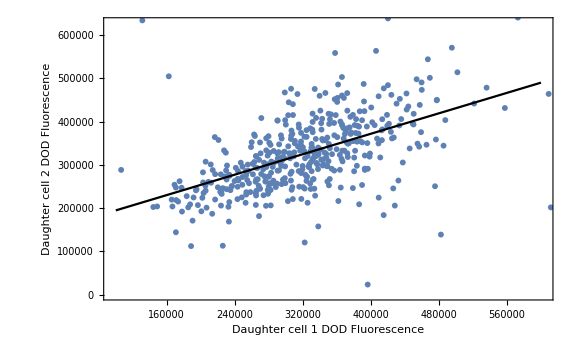

```mathematica
Show[ListPlot[
Transpose@{daughter227data[[All,5]],daughter227data[[All,6]]},
ImageSize-> Large,Frame->True,LabelStyle->Directive[Black,Medium],
FrameLabel->{"Daughter cell 1 DOD Fluorescence","Daughter cell 2 DOD Fluorescence"}],Plot[lm[x],{x,100000,600000},PlotStyle->Black]]
```

```mathematica
data=Map[{daughter227data⟦#,5⟧,daughter227data⟦#,6⟧}&,Range[2,450]];
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[135561.+0.591037 x]

```mathematica
N[Correlation[data[[All,1]],data[[All,2]]]]
```

0.532032

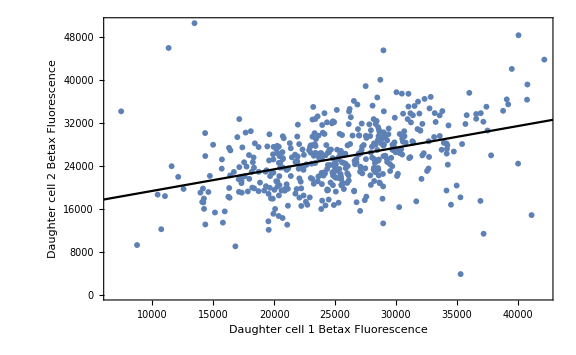

```mathematica
Show[ListPlot[
Transpose@{daughter227data[[All,8]],daughter227data[[All,9]]},
ImageSize-> Large,Frame->True,LabelStyle->Directive[Black,Medium],
FrameLabel->{"Daughter cell 1 Betax Fluorescence","Daughter cell 2 Betax Fluorescence"}],Plot[lmb[x],{x,0,45000},PlotStyle->Black]]
```

```mathematica
datab=Map[{daughter227data⟦#,8⟧,daughter227data⟦#,9⟧}&,Range[2,450]];
```

```mathematica
lmb=LinearModelFit[datab,x,x]
```

FittedModel[15271.2+0.402095 x]

```mathematica
N[Correlation[datab[[All,1]],datab[[All,2]]]]
```

0.398026